```mathematica
Needs["GeneralUtilities`"];

Get[FileNameJoin@{NotebookDirectory[],"analyticalReachabilitySolutions-utilities.m"}];
Get[FileNameJoin@{NotebookDirectory[],"stabilityAnalysis.m"}];
```

```mathematica
generalTwoColumnsStateWithD[nSites_]:=Join[
{{u[1],0}},
Table[
{u@site-d@site,d@site},
{site,Range[2,nSites-1]}
],
{{0,u[nSites]}}
];

MF[args___]:=MatrixForm[args];
traditionalForm[expr___]:=expr//Chop//TraditionalForm//Style[#,FontSize->20]&;
```

## Make analytical reachability conditions (build and test the functions generating the conditions)

```mathematica
reachabilitySolutions`verifyReachabilityConditions[4]
```

{Conjugate[u_(3,1)] u_(1,1)+Conjugate[u_(4,2)] u_(2,2)==0,Conjugate[u_(2,1)] u_(1,1)+Conjugate[u_(3,1)] u_(2,1)+Conjugate[u_(3,2)] u_(2,2)+Conjugate[u_(4,2)] u_(3,2)==0}

```mathematica
reachabilitySolutions`verifyReachabilityConditions[3]
```

{Conjugate[u_(2,1)] u_(1,1)+Conjugate[u_(3,2)] u_(2,2)==0}

```mathematica
reachabilitySolutions`verifyReachabilityConditions[3]//traditionalForm
reachabilitySolutions`verifyReachabilityConditions[4]//Column//traditionalForm
reachabilitySolutions`verifyReachabilityConditions[5]//Column//traditionalForm
```

{u_(1,1) Conjugate[(u_(2,1))]+u_(2,2) Conjugate[(u_(3,2))]==0}

u_(1,1) Conjugate[(u_(3,1))]+u_(2,2) Conjugate[(u_(4,2))]==0
u_(1,1) Conjugate[(u_(2,1))]+u_(2,1) Conjugate[(u_(3,1))]+u_(2,2) Conjugate[(u_(3,2))]+u_(3,2) Conjugate[(u_(4,2))]==0

u_(1,1) Conjugate[(u_(4,1))]+u_(2,2) Conjugate[(u_(5,2))]==0
u_(1,1) Conjugate[(u_(3,1))]+u_(2,1) Conjugate[(u_(4,1))]+u_(2,2) Conjugate[(u_(4,2))]+u_(3,2) Conjugate[(u_(5,2))]==0
u_(1,1) Conjugate[(u_(2,1))]+u_(2,1) Conjugate[(u_(3,1))]+u_(2,2) Conjugate[(u_(3,2))]+u_(3,1) Conjugate[(u_(4,1))]+u_(3,2) Conjugate[(u_(4,2))]+u_(4,2) Conjugate[(u_(5,2))]==0

Randomly generated states do not satisfy the reachability conditions (not even close!):

```mathematica
reachabilitySolutions`verifyReachabilityConditions/@Table[RandomComplex[{-1-I,1+I},{4,2}],{10}]//TableForm
```

-0.0866386+0.641875 ⅈ==0 | -0.601465-1.50066 ⅈ==0
0.487762-0.738948 ⅈ==0 | -0.743618+0.661147 ⅈ==0
0.592426+0.436577 ⅈ==0 | 0.902263-0.689824 ⅈ==0
0.338817-0.622823 ⅈ==0 | 0.242718-0.978259 ⅈ==0
1.85065+1.07058 ⅈ==0 | -0.991485-0.237738 ⅈ==0
-0.224911+0.193896 ⅈ==0 | 0.141627+0.236103 ⅈ==0
0.258557-0.0893965 ⅈ==0 | 0.224839-0.135411 ⅈ==0
0.522866+0.105808 ⅈ==0 | 2.26027-0.420388 ⅈ==0
-0.579825+0.462932 ⅈ==0 | 0.527207-0.374082 ⅈ==0
-0.795646+0.0852082 ⅈ==0 | -0.544049-0.611657 ⅈ==0

A state obtained in a QW evolution does:

```mathematica
Range[2,20]/.step_Integer:>With[{nSteps=step},
With[{
evolvedState=Partition[#,2]&@QWEvolve[{1,0},RandomReal[{0,2Pi},{nSteps,3}]]
},
And@@reachabilitySolutions`verifyReachabilityConditions[evolvedState]
]
]//TableForm
```

0==0
0==0&&0==0
0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0
0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0&&0==0

```mathematica
reachabilitySolutions`makeConditionsForDs[2,u/@Range@3,d]//traditionalForm

reachabilitySolutions`makeConditionsForDs[3,u/@Range@4,d]//Column//traditionalForm
```

{d(2) Conjugate[u(3)]+u(1) (Conjugate[u(2)]-Conjugate[d(2)])==0}

d(2) Conjugate[u(4)]+u(1) (Conjugate[u(3)]-Conjugate[d(3)])==0
d(3) Conjugate[u(4)]+u(1) (Conjugate[u(2)]-Conjugate[d(2)])+(u(2)-d(2)) (Conjugate[u(3)]-Conjugate[d(3)])+d(2) Conjugate[d(3)]==0

## Solve analytically equations for ds for 2 steps

```mathematica
reachabilitySolutions`makeConditionsForDs[2,u/@Range@3,d]//traditionalForm
reachabilitySolutions`makeConditionsForDs[2,RandomComplex[{-1-I,1+I},3],d]//traditionalForm
```

{d(2) Conjugate[u(3)]+u(1) (Conjugate[u(2)]-Conjugate[d(2)])==0}

{(0.345161+0.968565 ⅈ) d(2)-(0.806298+0.318353 ⅈ) (-Conjugate[d(2)]+(0.330975-0.767117 ⅈ))==0}

```mathematica
Solve[
reachabilitySolutions`makeConditionsForDs[2,u/@Range@3,d],
d[2]
]//FullSimplify
```

{{d[2]→(Abs[u[1]]^2 u[2]+Conjugate[u[2]] u[1] u[3])/(Abs[u[1]]^2-Abs[u[3]]^2)}}

### In the case |u_1|≠|u_2|:

#### Try to find and compute projection probabilities

Start by finding the solution for d:

```mathematica
solutionForTwoSteps=Solve[
d Conjugate@u[3]+u[1]Conjugate[u[2]-d]==0,
d
]//FullSimplify;
solutionForTwoSteps⟦1,1⟧/.u@s_:>Subscript[u, s]//TraditionalForm//Style[#,FontSize->20]&
(*MaTeX[solutionForTwoSteps⟦1,1⟧,Magnification->2]*)
```

d→(u_2 Abs[u_1]^2+u_1 u_3 Conjugate[(u_2)])/(Abs[u_1]^2-Abs[u_3]^2)

Call generalStateToGenerate the result of substituting the above expression for d inside the general matrix form of a state after 2 steps:

```mathematica
Set[generalStateToGenerate,
generalTwoColumnsStateWithD[2+1]//.{d[2]->d,solutionForTwoSteps⟦1,1⟧}//FullSimplify
]/.u@s_:>Subscript[u, s]//traditionalForm
```

(u_1 | 0
(u_2 Abs[u_3]^2+Conjugate[(u_2)] u_1 u_3)/(Abs[u_3]^2-Abs[u_1]^2) | (u_2 Abs[u_1]^2+Conjugate[(u_2)] u_1 u_3)/(Abs[u_1]^2-Abs[u_3]^2)
0 | u_3)

The above expression is however not normalized. Its norm is:

```mathematica
generalStateToGenerateNormalized=#/Norm@Flatten@#&@generalStateToGenerate;
Norm@Flatten@generalStateToGenerate/.u@s_:>Subscript[u, s]//TraditionalForm//Style[#,FontSize->20]&
```

√(Abs[(u_2 Abs[u_1]^2+Conjugate[(u_2)] u_1 u_3)/(Abs[u_1]^2-Abs[u_3]^2)]^2+Abs[(u_2 Abs[u_3]^2+Conjugate[(u_2)] u_1 u_3)/(Abs[u_3]^2-Abs[u_1]^2)]^2+Abs[u_1]^2+Abs[u_3]^2)

If we take the normalized version of the state, and project it over +, we immediately see that indeed we get the target state, up to a normalization factor:

```mathematica
(stateObtainedAfterProjection=Total[#]/(√2)&/@generalStateToGenerateNormalized)//FullSimplify
```

{u[1]/(√2 √(Abs[u[1]]^2+((-Abs[u[1]]^2 Abs[u[3]]+Abs[u[3]]^3)^2+Abs[Abs[u[1]]^2 u[2]+Conjugate[u[2]] u[1] u[3]]^2+Abs[Abs[u[3]]^2 u[2]+Conjugate[u[2]] u[1] u[3]]^2)/((Abs[u[1]]^2-Abs[u[3]]^2)^2))),u[2]/(√2 √(Abs[u[1]]^2+((-Abs[u[1]]^2 Abs[u[3]]+Abs[u[3]]^3)^2+Abs[Abs[u[1]]^2 u[2]+Conjugate[u[2]] u[1] u[3]]^2+Abs[Abs[u[3]]^2 u[2]+Conjugate[u[2]] u[1] u[3]]^2)/((Abs[u[1]]^2-Abs[u[3]]^2)^2))),u[3]/(√2 √(Abs[u[1]]^2+((-Abs[u[1]]^2 Abs[u[3]]+Abs[u[3]]^3)^2+Abs[Abs[u[1]]^2 u[2]+Conjugate[u[2]] u[1] u[3]]^2+Abs[Abs[u[3]]^2 u[2]+Conjugate[u[2]] u[1] u[3]]^2)/((Abs[u[1]]^2-Abs[u[3]]^2)^2)))}

The corresponding probability of the projection is the squared of the normalization factor above:

```mathematica
probabilityOfTheProjection=Power[stateObtainedAfterProjection⟦1⟧/u[1],2]
```

1/(2 (Abs[u[1]]^2+Abs[u[3]]^2+Abs[(Abs[u[1]]^2 u[2]+Conjugate[u[2]] u[1] u[3])/(Abs[u[1]]^2-Abs[u[3]]^2)]^2+Abs[(Abs[u[3]]^2 u[2]+Conjugate[u[2]] u[1] u[3])/(-Abs[u[1]]^2+Abs[u[3]]^2)]^2))

Remembering that all the calculations of this section hold under the assumption that |u_1|≠|u_3|, let us check the consistency of the above computed probability for u_1≈ u_2.
Result: total mess

```mathematica
probabilityOfTheProjection/.{u[3]->u[1]+ϵ}
```

1/(2 (Abs[u[1]]^2+Abs[ϵ+u[1]]^2+Abs[(Conjugate[u[2]] u[1] (ϵ+u[1])+Abs[u[1]]^2 u[2])/(Abs[u[1]]^2-Abs[ϵ+u[1]]^2)]^2+Abs[(Conjugate[u[2]] u[1] (ϵ+u[1])+Abs[ϵ+u[1]]^2 u[2])/(-Abs[u[1]]^2+Abs[ϵ+u[1]]^2)]^2))

```mathematica
probabilityOfTheProjection/.{u[3]->u[1]+ϵ}//FullSimplify
```

1/(2 (Abs[u[1]]^2+Abs[ϵ+u[1]]^2+(Abs[Conjugate[u[2]] u[1] (ϵ+u[1])+Abs[u[1]]^2 u[2]]^2+Abs[(ϵ+u[1])^2 (Conjugate[u[2]] u[1]+Conjugate[ϵ+u[1]] u[2])^2])/Abs[ϵ Conjugate[u[1]]+Conjugate[ϵ] (ϵ+u[1])]^2))

```mathematica
NMaximize[
{probabilityOfTheProjection,
u[1]^2+u[2]^2+u[3]^2==1,
Abs@u[1]>.1,Abs@u[2]>.1,Abs@u[3]>.1
},
{u[1],u[2],u[3]}
]
```

{0.980392,{u[1]→0.1,u[2]→0.989949,u[3]→-0.1}}

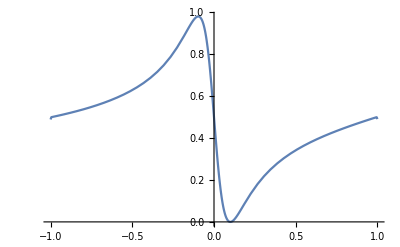

```mathematica
With[{u1=0.1},
Plot[
probabilityOfTheProjection/.{u[1]->u1,u[2]->√(1-u1^2-u[3]^2)},
{u[3],-1,1}
]
]
```

```mathematica
Manipulate[
Plot[
probabilityOfTheProjection/.{u[1]->u1,u[2]->√(1-u1^2-u[3]^2)},
{u[3],-√(1-u1^2),√(1-u1^2)},
PlotRange->{{-1,1},{0,1}}
],
{{u1,0.1},-1,1,Appearance->"Labeled"},
SynchronousUpdating->True
]
```

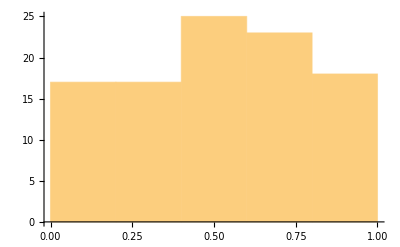

```mathematica
Table[
probabilityOfTheProjection/.{u[3]->u[1]+.0001}//replaceVars[u_],
100
]//Histogram
```

```mathematica
RandomPoint[Disk[]]
```

{-0.190865,0.0966627}

```mathematica
randomInRadius[r_]:=#⟦1⟧+I #⟦2⟧&@RandomPoint[Disk[{0,0},r]]
randomOnRadius[r_]:=#⟦1⟧+I #⟦2⟧&@FromPolarCoordinates[{
r,RandomReal[{-Pi,Pi}]
}]
```

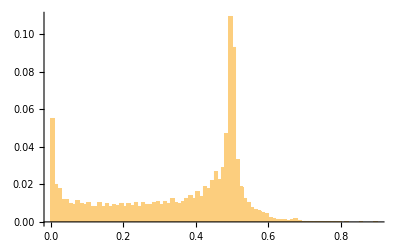

```mathematica
Histogram[
Table[
Block[{u1,u2,u3},
u1=randomInRadius[1];
u2=randomInRadius[√(1-Abs[u1]^2)];
u3=randomOnRadius[√(1-Abs[u1]^2-Abs[u2]^2)];
probabilityOfTheProjection/.{u[1]->u1,u[2]->u2,u[3]->u3}
],
10000
],
80,"Probability"
]
```

#### A step back. Let’s now compute the projection probability analytically in the case of real target, with u_3≥0, and study the resulting landscape

```mathematica
expr=FullSimplify[
1/(u[1]^2+(u[2]-d)^2+d^2+1-u[1]^2-u[2]^2)/2/.d->(u[1](Conjugate@u[1] u[2]+Conjugate@u[2] u[3]))/(Abs[u[1]]^2-Abs[u[3]]^2),
u[_]∈Reals
]/.u[3]->√(1-u[1]^2-u[2]^2)//Simplify
```

((u[1]-√(1-u[1]^2-u[2]^2))^2)/(2 (-1+u[2]^2) (-1+2 u[1] √(1-u[1]^2-u[2]^2)))

```mathematica
With[{
expr=Abs[(u[1](Conjugate@u[1] u[2]+Conjugate@u[2] u[3]))/(Abs[u[1]]^2-Abs[u[3]]^2)]/.u[3]->√I √(1-u[1]^2-u[2]^2)
},
Plot3D[expr,
{u[1],u[2]}∈Disk[],
PlotRange->{Automatic,Automatic,{-5,10}},PlotPoints->100,MaxRecursion->3,
ColorFunction->"TemperatureMap",ImageSize->Large
]
]
```

-Graphics3D-

```mathematica
With[{
expr=(u[1](Conjugate@u[1] u[2]+Conjugate@u[2] u[3]))/(Abs[u[1]]^2-Abs[u[3]]^2)/.u[3]->√(1-u[1]^2-u[2]^2)
},
Plot3D[expr,
{u[1],-1,1},
{u[2],-1,1},
PlotRange->{Automatic,Automatic,{-2,2}},PlotPoints->100,MaxRecursion->3,
ColorFunction->"TemperatureMap",ImageSize->Large
]
]
```

-Graphics3D-

```mathematica
figToSave=Block[{func},
func[r_?NumericQ,θ_?NumericQ]:=((u[1]-√(1-u[1]^2-u[2]^2))^2)/(2 (-1+u[2]^2) (-1+2 u[1] √(1-u[1]^2-u[2]^2)))/.{u[1]->x,u[2]->y}/.{x->r Cos[θ],y->r Sin[θ]}//FullSimplify//Evaluate;
ParametricPlot3D[
{r Cos[θ],r Sin[θ],func[r,θ]},
{r,0,1},{θ,0,2Pi},
PlotRange->All,PlotPoints->150,MaxRecursion->6,
ColorFunction->"TemperatureMap",ImageSize->Large,
AxesStyle->texStyles["title"],AxesLabel->{Subscript[u, 1],Subscript[u, 2],p}
]
]
```

-Graphics3D-

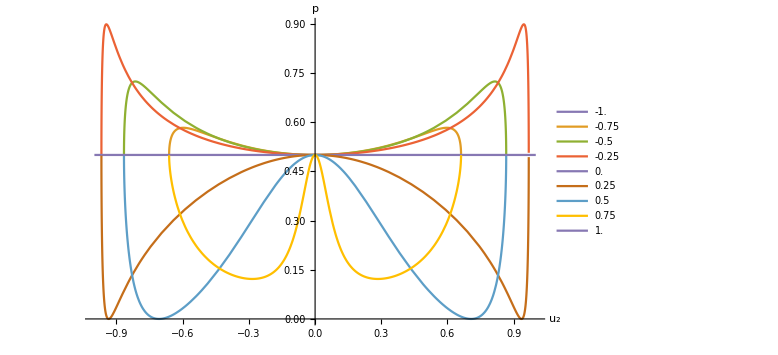

```mathematica
figToSave=With[{expr=((u[1]-√(1-u[1]^2-u[2]^2))^2)/(2 (-1+u[2]^2) (-1+2 u[1] √(1-u[1]^2-u[2]^2))),probedValues=N@Range[-1,1,1/4]},
Plot[
Evaluate[
expr/.u[1]->#&/@probedValues
],
{u[2],-1,1},
PlotRange->All,ImageSize->Large,
PlotLegends->probedValues,
PlotStyle->{RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.528488, 0.470624, 0.701351]},
PlotPoints->40,MaxRecursion->10,
AxesLabel->{Subscript[u, 2],p},
AxesStyle->texStyles["title"]
]
]
```

### Degenerate case u_1=u_3:

#### Look for analytical solutions (mess)

```mathematica
reducedEqs=Reduce[
d Conjugate@u[1]+u[1]Conjugate[u[2]-d]==0,
d
]//FullSimplify;
```

```mathematica
FullSimplify[reducedEqs,And[
u[1]≠0,
Re[u[1]]≠0
]
]
```

(Im[u[1]]==0&&(d==Re[d]||Im[u[2]]≠0)&&(2 Im[d]==Im[u[2]]||Im[u[2]]==0)&&Re[u[2]]==0)||(Im[u[1]]≠0&&((Im[u[1]] Re[d]==Im[d] Re[u[1]]&&u[2]==0)||(Im[u[2]]≠0&&Re[u[2]]≠0&&2 Conjugate[d] u[1]+Conjugate[u[1]] u[2]==2 d Conjugate[u[1]]+Conjugate[u[2]] u[1]&&Conjugate[u[2]] u[1]+Conjugate[u[1]] u[2]==0)))

```mathematica
List@@reducedEqs//Column
```

Im[u[1]]==0&&(u[1]==0||((d==Re[d]||Im[u[2]]≠0)&&(2 Im[d]==Im[u[2]]||Im[u[2]]==0)&&Re[u[2]]==0))
Im[u[1]]≠0&&Re[u[1]]≠0&&((Im[u[1]] Re[d]==Im[d] Re[u[1]]&&u[2]==0)||(Im[u[2]]≠0&&Re[u[2]]≠0&&2 Conjugate[d] u[1]+Conjugate[u[1]] u[2]==2 d Conjugate[u[1]]+Conjugate[u[2]] u[1]&&Conjugate[u[2]] u[1]+Conjugate[u[1]] u[2]==0))
Im[u[2]]==0&&(Re[d]==0||u[2]≠0)&&(2 Re[d]==u[2]||u[2]==0)&&Re[u[1]]==0

```mathematica
FullSimplify[reducedEqs,And[
u[1]≠0,
Re[u[1]]≠0,Im[u[1]]≠0
]
]
```

(Im[u[1]] Re[d]==Im[d] Re[u[1]]&&u[2]==0)||(Im[u[2]]≠0&&Re[u[2]]≠0&&2 Conjugate[d] u[1]+Conjugate[u[1]] u[2]==2 d Conjugate[u[1]]+Conjugate[u[2]] u[1]&&Conjugate[u[2]] u[1]+Conjugate[u[1]] u[2]==0)

```mathematica
2 Conjugate[d] u[1]+Conjugate[u[1]] u[2]==2 d Conjugate[u[1]]+Conjugate[u[2]] u[1]//FullSimplify
```

2 Conjugate[d] u[1]+Conjugate[u[1]] u[2]==2 d Conjugate[u[1]]+Conjugate[u[2]] u[1]

#### Compute stability of solutions

```mathematica
Block[{targetState,targetStateAsMatrix,initialState,coinParameters,fidelity,ϵ},
targetState=Normalize@{0.5ⅈ,0.2,0.5ⅈ}//Echo[#,"Target state:",MF]&;

targetStateAsMatrix=With[{u1I=Im@targetState⟦1⟧,u2R=Re@targetState⟦2⟧},
{
{u1I ⅈ,0},
{u2R/2+ⅈ dI,u2R/2-ⅈ dI},
{0,u1I ⅈ}
}//#/Norm@Flatten@#&//#/.dI->4&
]//Echo[#,"Final state:",MF]&;

coinParameters=devolveStateAllTheWayAndGetCoins[targetStateAsMatrix]["Coins"];
coinParameters={coinParameters⟦1⟧,Transpose@{#⟦1⟧,I #⟦2⟧}&@Transpose@coinParameters⟦2⟧};

coinParameters=unitaryToCoinPars/@coinParameters;
(*coinParameters=ReplacePart[coinParameters,{2,3}->0];*)
coinParameters//Echo[#,"Coin parameters:",MF]&;

fidelity[ϵ_,{indexParToChange__}]:=QFidelity[
Chop@Dot[
QWManyStepsEvolutionMatrix[2,
ReplacePart[coinParameters,
{indexParToChange}:>ϵ coinParameters⟦indexParToChange⟧
]
],
SparseArray[1->1,6]
]//Partition[#,2]&//Map@Total//Normalize,
targetState
];

Plot[
{fidelity[ϵ,{1,1}],
fidelity[ϵ,{2,1}],
fidelity[ϵ,{2,2}]},
{ϵ,.5,1.5},
PlotRange->All,PlotLegends->Automatic
]
]
```

Target state: (0.+0.680414 ⅈ
0.272166
0.+0.680414 ⅈ)

Final state: ((0.+0.680414 ⅈ)/(√(0.925926+Abs[0.136083-ⅈ dI]^2+Abs[0.136083+ⅈ dI]^2)) | 0
(0.136083+ⅈ dI)/(√(0.925926+Abs[0.136083-ⅈ dI]^2+Abs[0.136083+ⅈ dI]^2)) | (0.136083-ⅈ dI)/(√(0.925926+Abs[0.136083-ⅈ dI]^2+Abs[0.136083+ⅈ dI]^2))
0 | (0.+0.680414 ⅈ)/(√(0.925926+Abs[0.136083-ⅈ dI]^2+Abs[0.136083+ⅈ dI]^2)))

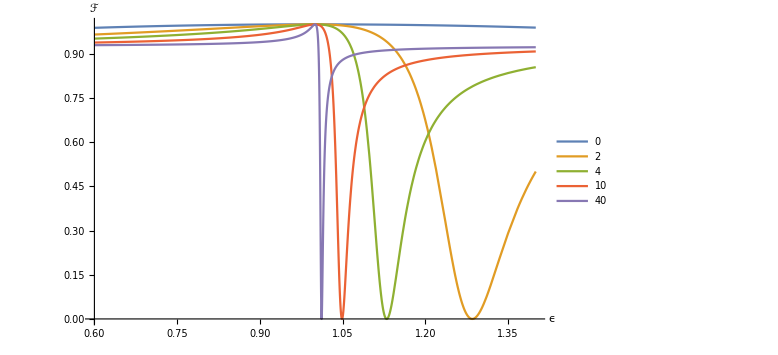

```mathematica
Block[{targetState,targetStateAsMatrix,initialState,coinParameters,fidelity,ϵ},
targetState=Normalize@{0.5ⅈ,0.2,0.5ⅈ}//Echo[#,"Target state:",MF]&;

targetStateAsMatrix=With[{u1I=Im@targetState⟦1⟧,u2R=Re@targetState⟦2⟧},
{
{u1I ⅈ,0},
{u2R/2+ⅈ dI,u2R/2-ⅈ dI},
{0,u1I ⅈ}
}//#/Norm@Flatten@#&
]//Echo[#,"Final state:",MF]&;

coinParameters=Map[
unitaryToCoinPars/@devolveStateAllTheWayAndGetCoins[#]["Coins"]&
][
targetStateAsMatrix/.{dI->#}&/@{0,2,4,10,40}
];

fidelity[ϵ_,idx_]:=QFidelity[
Chop@Dot[
manyStepsEvolutionMatrix[2,
ReplacePart[coinParameters⟦idx⟧,
{2,1}:>ϵ coinParameters⟦idx⟧⟦2,1⟧
]
],
SparseArray[1->1,6]
]//Partition[#,2]&//Map@Total//Normalize,
targetState
];

figToSave=Plot[
{fidelity[ϵ,1],
fidelity[ϵ,2],
fidelity[ϵ,3],
fidelity[ϵ,4],
fidelity[ϵ,5]},
{ϵ,.6,1.4},
PlotRange->All,PlotLegends->({0,2,4,10,40}/.s_Integer:>Style[s,{FontFamily->"CMU Serif",FontSize->24,FontWeight->Plain,FontSlant->Plain}]),
ImageSize->Large,AxesStyle->texStyles["title"],AxesLabel->{ϵ,ℱ}
]
]
```

```mathematica
exportHere["fidelityVsEpsVaryingD_2steps.pdf",figToSave]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\fidelityVsEpsVaryingD_2steps.pdf

Target state: (0.+0.680414 ⅈ
0.272166
0.+0.680414 ⅈ)

Final state: ((0.+0.680414 ⅈ)/(√(0.925926+Abs[0.136083-ⅈ dI]^2+Abs[0.136083+ⅈ dI]^2)) | 0
(0.136083+ⅈ dI)/(√(0.925926+Abs[0.136083-ⅈ dI]^2+Abs[0.136083+ⅈ dI]^2)) | (0.136083-ⅈ dI)/(√(0.925926+Abs[0.136083-ⅈ dI]^2+Abs[0.136083+ⅈ dI]^2))
0 | (0.+0.680414 ⅈ)/(√(0.925926+Abs[0.136083-ⅈ dI]^2+Abs[0.136083+ⅈ dI]^2)))

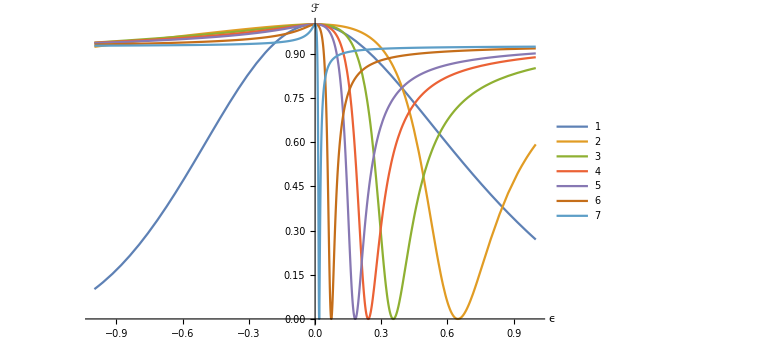

```mathematica
Block[{targetState,targetStateAsMatrix,initialState,coinParameters,fidelity,ϵ},
targetState=Normalize@{0.5ⅈ,0.2,0.5ⅈ}//Echo[#,"Target state:",MF]&;

targetStateAsMatrix=With[{u1I=Im@targetState⟦1⟧,u2R=Re@targetState⟦2⟧},
{
{u1I ⅈ,0},
{u2R/2+ⅈ dI,u2R/2-ⅈ dI},
{0,u1I ⅈ}
}//#/Norm@Flatten@#&
]//Echo[#,"Final state:",MF]&;

coinParameters=Map[
unitaryToCoinPars/@devolveStateAllTheWayAndGetCoins[#]["Coins"]&
][
targetStateAsMatrix/.{dI->#}&/@{0,1,2,3,4,10,40}
];

fidelity[ϵ_,idx_]:=QFidelity[
Chop@Dot[
manyStepsEvolutionMatrix[2,
ReplacePart[coinParameters⟦idx⟧,
{2,1}:>ϵ+coinParameters⟦idx⟧⟦2,1⟧
]
],
SparseArray[1->1,6]
]//Partition[#,2]&//Map@Total//Normalize,
targetState
];

Plot[
{fidelity[ϵ,1],
fidelity[ϵ,2],
fidelity[ϵ,3],
fidelity[ϵ,4],
fidelity[ϵ,5],
fidelity[ϵ,6],
fidelity[ϵ,7]},
{ϵ,-1,1},
PlotRange->All,PlotLegends->Automatic,
ImageSize->Large,AxesStyle->texStyles["title"],AxesLabel->{ϵ,ℱ}
]
]
```

### Degenerate case u_1=-u_3:

```mathematica
reducedEqs=Reduce[
-d Conjugate@u[1]+u[1]Conjugate[u[2]-d]==0,
d
]//FullSimplify;
```

```mathematica
reducedEqs
```

(Re[u[2]]==0&&((2 Im[d]==Im[u[2]]&&Im[u[2]]≠0&&Re[u[1]]==0)||((Im[u[1]]≠0||Re[d]==0)&&(Im[u[1]]==0||d Conjugate[u[1]]+Conjugate[d] u[1]==0)&&Im[u[2]]==0)))||(Im[u[1]]==0&&((Im[u[2]]==0&&2 Re[d]==u[2]&&u[2]≠0)||u[1]==0))||(Im[u[1]]≠0&&Im[u[2]]≠0&&Im[u[1]] Im[u[2]]+Re[u[1]] Re[-2 d+u[2]]==2 Im[d] Im[u[1]]&&Re[u[2]]≠0&&Re[u[2]] u[1]==Re[u[1]] u[2])

```mathematica
reducedEqs//Apply@List//TableForm
```

Re[u[2]]==0&&((2 Im[d]==Im[u[2]]&&Im[u[2]]≠0&&Re[u[1]]==0)||((Im[u[1]]≠0||Re[d]==0)&&(Im[u[1]]==0||d Conjugate[u[1]]+Conjugate[d] u[1]==0)&&Im[u[2]]==0))
Im[u[1]]==0&&((Im[u[2]]==0&&2 Re[d]==u[2]&&u[2]≠0)||u[1]==0)
Im[u[1]]≠0&&Im[u[2]]≠0&&Im[u[1]] Im[u[2]]+Re[u[1]] Re[-2 d+u[2]]==2 Im[d] Im[u[1]]&&Re[u[2]]≠0&&Re[u[2]] u[1]==Re[u[1]] u[2]

### Degenerate case u_3=u_1 ⅇ^(ⅈ ϕ):

```mathematica
reducedEqs=Reduce[
-d Conjugate[u[1]]I+u[1]Conjugate[u[2]-d]==0,
d
]//FullSimplify;
```

```mathematica
reducedEqs//Apply@List//TableForm
```

Im[u[1]]==0&&((Im[d]==Re[d]&&u[2]==0)||(Im[d]==Im[u[2]]+Re[d]&&Im[u[2]]≠0&&Im[u[2]]+Re[u[2]]==0)||u[1]==0)
Im[u[1]]≠0&&((Im[d]+Re[(Im[u[2]]+Re[d]) u[1]+Im[u[1]] (d-u[2])]/(Im[u[1]]-Re[u[1]])==0&&Im[u[2]]≠0&&Re[u[1]]==Im[u[1]] (1-(2 Im[u[2]])/(Im[u[2]]+Re[u[2]]))&&Im[u[2]]+Re[u[2]]≠0)||(Im[u[2]]==0&&((Im[u[1]]==Re[u[1]]&&(Re[d]==0||u[2]≠0)&&(Re[d]==(Im[u[1]] u[2])/(Im[u[1]]+Re[u[1]])||u[2]==0))||(Im[u[1]] (Im[d]+Re[d])+Re[d] Re[u[1]]==Im[d] Re[u[1]]&&u[2]==0&&Im[u[1]]≠Re[u[1]]))))

## Solve numerically the system of equations for the ds, for more steps

The function reachabilitySolutions`findDsGivingReachableState can be used to find numerically the solution to the system of equations for the parameters d.
When the first argument is an integer, it is assumed to be the number of steps considered. The second argument is the name of the parameter to be used in the output.
With no target state specified the equations are solved for a randomly chosen target state.

(note: for 4 and 5 steps it can take a few minutes to get the results)

```mathematica
reachabilitySolutions`findDsGivingReachableState[2,d]//Quiet//MF
reachabilitySolutions`findDsGivingReachableState[3,d]//Quiet//MF
reachabilitySolutions`findDsGivingReachableState[4,d]//Quiet//MF
reachabilitySolutions`findDsGivingReachableState[5,d]//Quiet//MF
```

(d[2]→-0.0228326+0.461623 ⅈ)

(d[2]→-0.331752+0.174496 ⅈ | d[3]→-1.11768-0.736641 ⅈ
d[2]→0.158678-0.115463 ⅈ | d[3]→0.259137-0.553952 ⅈ)

(d[2]→-0.245007+0.482176 ⅈ | d[3]→-0.0371249-2.11795 ⅈ | d[4]→-0.184117-0.59651 ⅈ
d[2]→-0.0944685-0.0604659 ⅈ | d[3]→-1.49597+0.171665 ⅈ | d[4]→0.379605-0.121883 ⅈ
d[2]→0.102429-0.126449 ⅈ | d[3]→0.107686-0.212072 ⅈ | d[4]→0.640987-0.196204 ⅈ)

(d[2]→-0.118239+0.302308 ⅈ | d[3]→-0.671894-0.348119 ⅈ | d[4]→0.00969016+0.419423 ⅈ | d[5]→0.448379-0.0999115 ⅈ
d[2]→0.0156232-0.264051 ⅈ | d[3]→0.331231+0.362343 ⅈ | d[4]→0.0295238-0.05463 ⅈ | d[5]→-0.048547-0.407898 ⅈ
d[2]→0.0852433-0.0326236 ⅈ | d[3]→-0.384786+0.226339 ⅈ | d[4]→0.467762-0.371432 ⅈ | d[5]→0.066063-0.193874 ⅈ
d[2]→0.225386-0.244232 ⅈ | d[3]→0.360895-0.188637 ⅈ | d[4]→-0.359336-0.1378 ⅈ | d[5]→-0.183724-0.245024 ⅈ
d[2]→0.29584-0.0118208 ⅈ | d[3]→-0.172229-0.104667 ⅈ | d[4]→0.0561115-0.743227 ⅈ | d[5]→-0.0690088-0.029708 ⅈ
d[2]→0.430937-0.580863 ⅈ | d[3]→-0.525757-0.425912 ⅈ | d[4]→-0.156408+0.482918 ⅈ | d[5]→-0.568716-0.338728 ⅈ)

6 steps computation stopped after ~1 hour

```mathematica
reachabilitySolutions`findDsGivingReachableState[6,d]//Quiet//MF
```

## Solutions for special targets

The function reachabilitySolutions`findDsGivingReachableState can also be used to solve for a specific target state. Just use the corresponding amplitudes as first argument.

```mathematica
Quiet@reachabilitySolutions`findDsGivingReachableState[Normalize@RandomReal[{0,1},3],d]
```

{{d[2]→1.11089}}

```mathematica
Quiet@reachabilitySolutions`findDsGivingReachableState[Normalize@{1,1,1},d]
Quiet@reachabilitySolutions`findDsGivingReachableState[Normalize@{1.1,1,1},d]
```

{}

{{d[2]→6.1396}}

```mathematica
reachabilitySolutions`findDsGivingReachableState[{1,1,1,1},d]
```

{{d[2]→0.-0.5 ⅈ,d[3]→0.5+0.5 ⅈ},{d[2]→0.+0.5 ⅈ,d[3]→0.5-0.5 ⅈ}}

```mathematica
reachabilitySolutions`findDsGivingReachableState[ConstantArray[1,6],d]//MF
```

(d[2]→0.429566 | d[3]→-0.645991 | d[4]→0.66625 | d[5]→0.837814
d[2]→-0.429566 | d[3]→-0.258002 | d[4]→1.05424 | d[5]→-0.0213174
d[2]→0.+0.530531 ⅈ | d[3]→0.68944+0.157075 ⅈ | d[4]→-0.281192-0.157075 ⅈ | d[5]→0.408248-0.530531 ⅈ
d[2]→0.-0.530531 ⅈ | d[3]→0.68944-0.157075 ⅈ | d[4]→-0.281192+0.157075 ⅈ | d[5]→0.408248+0.530531 ⅈ
d[2]→0.+0.117988 ⅈ | d[3]→0.0341+0.706284 ⅈ | d[4]→0.374148-0.706284 ⅈ | d[5]→0.408248-0.117988 ⅈ
d[2]→0.-0.117988 ⅈ | d[3]→0.0341-0.706284 ⅈ | d[4]→0.374148+0.706284 ⅈ | d[5]→0.408248+0.117988 ⅈ)

```mathematica
reachabilitySolutions`computeFullStatesFromTarget[{1,1,1,1,1,1}]//Map@MF
```

{(0.219986 | 0
-0.011487 | 0.231473
0.568081 | -0.348095
-0.139025 | 0.359012
-0.231473 | 0.45146
0 | 0.219986),(0.219986 | 0
0.45146 | -0.231473
0.359012 | -0.139025
-0.348095 | 0.568081
0.231473 | -0.011487
0 | 0.219986),(0.235702 | 0
0.235702-0.306302 ⅈ | 0.+0.306302 ⅈ
-0.162346-0.0906876 ⅈ | 0.398048+0.0906876 ⅈ
0.398048+0.0906876 ⅈ | -0.162346-0.0906876 ⅈ
0.+0.306302 ⅈ | 0.235702-0.306302 ⅈ
0 | 0.235702),(0.235702 | 0
0.235702+0.306302 ⅈ | 0.-0.306302 ⅈ
-0.162346+0.0906876 ⅈ | 0.398048-0.0906876 ⅈ
0.398048-0.0906876 ⅈ | -0.162346+0.0906876 ⅈ
0.-0.306302 ⅈ | 0.235702+0.306302 ⅈ
0 | 0.235702),(0.235702 | 0
0.235702-0.0681206 ⅈ | 0.+0.0681206 ⅈ
0.216015-0.407773 ⅈ | 0.0196876+0.407773 ⅈ
0.0196876+0.407773 ⅈ | 0.216015-0.407773 ⅈ
0.+0.0681206 ⅈ | 0.235702-0.0681206 ⅈ
0 | 0.235702),(0.235702 | 0
0.235702+0.0681206 ⅈ | 0.-0.0681206 ⅈ
0.216015+0.407773 ⅈ | 0.0196876-0.407773 ⅈ
0.0196876-0.407773 ⅈ | 0.216015+0.407773 ⅈ
0.-0.0681206 ⅈ | 0.235702+0.0681206 ⅈ
0 | 0.235702)}

```mathematica
reachabilitySolutions`computeProbabilitiesFromTarget@{1,1,1,1,1,-1}
```

{0.350117,0.350117,0.340265,0.340265,0.340265,0.340265}

```mathematica
reachabilitySolutions`computeProbabilitiesFromTarget@{1,1,1,1,1,I}
```

{0.194887,0.182773,0.182773,0.200807,0.200807,0.194887}

```mathematica
reachabilitySolutions`findDsGivingReachableState[{1,1,1,1}]⟦All,All,2⟧//MF
reachabilitySolutions`computeFullStatesFromTarget[{1,1,1,1}]//Map@MF
reachabilitySolutions`computeProbabilitiesFromTarget[{1,1,1,1}]
```

(0.-0.5 ⅈ | 0.5+0.5 ⅈ
0.+0.5 ⅈ | 0.5-0.5 ⅈ)

{(0.353553 | 0.
0.353553+0.353553 ⅈ | 0.-0.353553 ⅈ
0.-0.353553 ⅈ | 0.353553+0.353553 ⅈ
0. | 0.353553),(0.353553 | 0.
0.353553-0.353553 ⅈ | 0.+0.353553 ⅈ
0.+0.353553 ⅈ | 0.353553-0.353553 ⅈ
0. | 0.353553)}

{0.25,0.25}

```mathematica
reachabilitySolutions`computeProbabilitiesFromTarget[{1,1,1,1}]⟦1⟧
stabilityAnalysis`plotFidelityVsParameters[
Reverse@QWComputeCoinParametersFromState@#,
Normalize@{1,1,1,1},
{.9,1.1},
"TypeOfPerturbation"->Times,
"ParametersToPlot"->{1,2,3},
"HighlightZeros"->True,
PlotRange->All,ImageSize->Large
]&[
reachabilitySolutions`computeFullStatesFromTarget[{1,1,1,1}]⟦1⟧
]
```

0.25

-Graphics-

```mathematica
reachabilitySolutions`computeProbabilitiesFromTarget[{1,1,1,1,1,1}]⟦6⟧
```

0.166667

```mathematica
fig=stabilityAnalysis`plotFidelityVsParameters[
Reverse@Chop@QWComputeCoinParametersFromState@#,
Normalize@{1,1,1,1,1,1},
{.9,1.1},
"TypeOfPerturbation"->Times,
"ParametersToPlot"->{1,3},
PlotRange->All,ImageSize->Large
]&[
reachabilitySolutions`computeFullStatesFromTarget[{1,1,1,1,1,1}]⟦6⟧
]
```

-Graphics-

## Given a final state, compute the set of coin operators generating it, and the associated probabilities

```mathematica
data2StepsSorted=Join@@(Import/@FileNames[FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_2steps_*.mx"}]);
data3StepsSorted=Join@@(Import/@FileNames[FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_3steps_*.mx"}]);
data4StepsSorted=Join@@(Import/@FileNames[FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_4steps_*.mx"}]);
data5StepsSorted=Join@@(Import/@FileNames[FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_5steps_*.mx"}]);
```

### For 2 steps, compute the probability associated with all the solutions for the d:

#### Generate/save/load data

```mathematica
data2Steps=With[{numberOfSteps=2,numberOfStatesToCompute=10000},
Block[{randomTarget,solutionsForD,wholeStateWithDs,fullStatesFromTarget,iterator=0},
Table[
iterator++;
randomTarget=RandomUnitary[numberOfSteps+1]⟦1⟧;
solutionsForD=Quiet@findDsGivingReachableState[numberOfSteps, randomTarget];
wholeStateWithDs=generalTwoColumnsStateWithD[numberOfSteps+1]/.Thread[u/@Range@Length@randomTarget->randomTarget];

(* Compute full state for every solution found for the ds *)
fullStatesFromTarget=Function[indexOfSolution,
wholeStateWithDs/.solutionsForD⟦indexOfSolution⟧//#/Norm@Flatten@#&
]/@Range@Length@solutionsForD;

(* prepare output of iteration *)
<|
"Probabilities"->projectionProbabilityFromWholeState/@fullStatesFromTarget,
"TargetState"->randomTarget,
"WholeStates"->fullStatesFromTarget
|>,
numberOfStatesToCompute
]~Monitor~iterator
]
];
data2StepsSorted=Normal@Dataset[data2Steps][SortBy[Min@#"Probabilities"&]];
```

Careful here! This exports the data, potentially overwriting other data!

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"data","statesAndProbabilities_2steps_10000states_201703012_2.mx"},data2StepsSorted,"MX"]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\statesAndProbabilities_2steps_10000states_201703012_2.mx

```mathematica
FileNames@FileNameJoin@{NotebookDirectory[],"data","statesAndProbabilities_2steps*.mx"}
```

{C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\statesAndProbabilities_2steps_10000states_201703012_2.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\statesAndProbabilities_2steps_10000states_201703012.mx}

Use the following to load data from the files

```mathematica
data2StepsSorted=Join@@(Import/@FileNames@FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_2steps*.mx"});
```

```mathematica
data2StepsSorted⟦1⟧
```

<|Probabilities→{5.63664×10^-8},TargetState→{-0.656042-0.113556 ⅈ,-0.283263+0.181797 ⅈ,-0.413764+0.521751 ⅈ},WholeStates→{{{-0.000220271-0.0000381273 ⅈ,0.},{-0.660708+0.252077 ⅈ,0.660613-0.252016 ⅈ},{0.,-0.000138924+0.000175182 ⅈ}}}|>

#### Do stuff with it

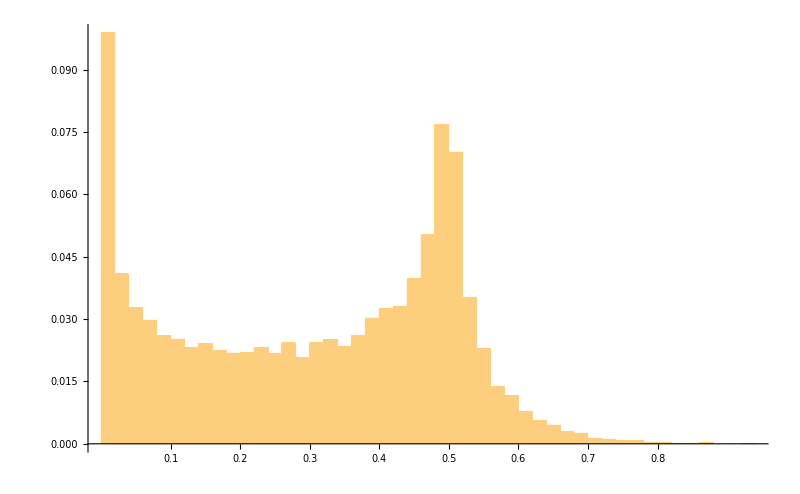

```mathematica
Histogram[
First/@data2StepsSorted⟦All,"Probabilities"⟧,
40,"Probability",
AxesStyle->texStyles["title"],ImageSize->800,
Ticks->{Range[.1,.8,.1],Automatic}
]
```

```mathematica
exportHere["projectionProbabilities_2steps_20000states_histogram40binsProbability.pdf",%297]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\projectionProbabilities_2steps_20000states_histogram40binsProbability.pdf

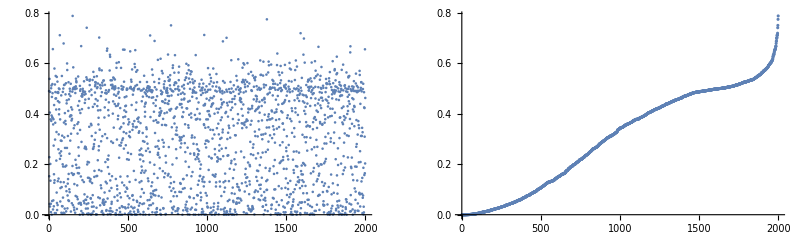

```mathematica
GraphicsRow@{
data2Steps⟦All,"Probabilities",1⟧//ListPlot,
data2StepsSorted⟦All,"Probabilities",1⟧//ListPlot
}
```

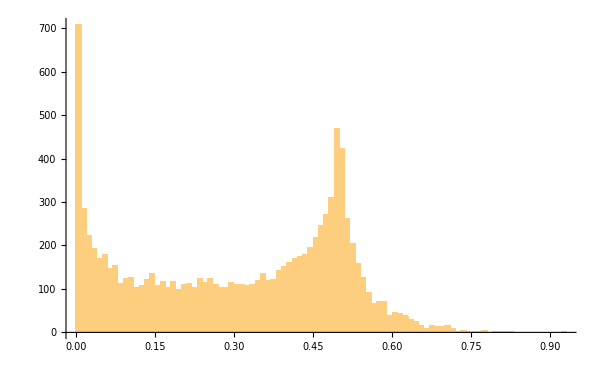

```mathematica
Histogram[
data2Steps⟦All,"Probabilities",1⟧,
80,
AxesStyle->texStyles["title"],ImageSize->600
]
```

```mathematica
exportHere["maxProjectionProbabilities_2steps_10000states_histogram.pdf",%59]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\maxProjectionProbabilities_2steps_10000states_histogram.pdf

```mathematica
SystemOpen@%
```

The states corresponding to very low probabilities turn out to have a very specific form: they all correspond to targets with |u_1|≃|u_3|, with the reconstructed full states being basically vanishing in the first and third row, and with opposite elements in the second row. That is, the full states are basically 2⊗-.

```mathematica
data2StepsSorted⟦1;;10,"Probabilities",1⟧
```

{4.94119×10^-7,2.26661×10^-6,6.55379×10^-6,9.11585×10^-6,0.0000120407,0.0000145253,0.0000223985,0.000027202,0.0000273769,0.0000277396}

```mathematica
data2StepsSorted⟦1;;10,"TargetState"⟧//absArgForm//MF
```

(0.641006 ⅇ^(2.23037ⅈ) | 0.42274 ⅇ^(2.21808ⅈ) | 0.640627 ⅇ^(2.01505ⅈ)
0.672124 ⅇ^(1.89125ⅈ) | 0.311686 ⅇ^(-2.32287ⅈ) | 0.67164 ⅇ^(1.13745ⅈ)
0.615296 ⅇ^(0.0589266ⅈ) | 0.493592 ⅇ^(-0.589013ⅈ) | 0.614637 ⅇ^(1.02914ⅈ)
0.565194 ⅇ^(1.01932ⅈ) | 0.599079 ⅇ^(-1.96581ⅈ) | 0.567151 ⅇ^(0.734302ⅈ)
0.58094 ⅇ^(-2.1696ⅈ) | 0.568079 ⅇ^(-1.6078ⅈ) | 0.58292 ⅇ^(-2.10412ⅈ)
0.617545 ⅇ^(-2.38202ⅈ) | 0.489903 ⅇ^(0.525169ⅈ) | 0.615332 ⅇ^(-2.29159ⅈ)
0.447947 ⅇ^(0.601486ⅈ) | 0.77555 ⅇ^(1.52229ⅈ) | 0.444821 ⅇ^(3.05373ⅈ)
0.549378 ⅇ^(-0.245672ⅈ) | 0.632615 ⅇ^(0.321536ⅈ) | 0.545878 ⅇ^(0.385748ⅈ)
0.559562 ⅇ^(1.29741ⅈ) | 0.609755 ⅇ^(-2.42229ⅈ) | 0.561328 ⅇ^(-1.96721ⅈ)
0.481856 ⅇ^(0.486994ⅈ) | 0.730971 ⅇ^(0.108197ⅈ) | 0.483214 ⅇ^(-2.66404ⅈ))

To better assess this property of low projection probabilities being associated to equal moduli of 1st and 3rd site, we plot (|u_1|)/(|u_3|) for all target states, in order of increasing projection probability.
Notice how all the states with low projection probability correspond to a value 1.

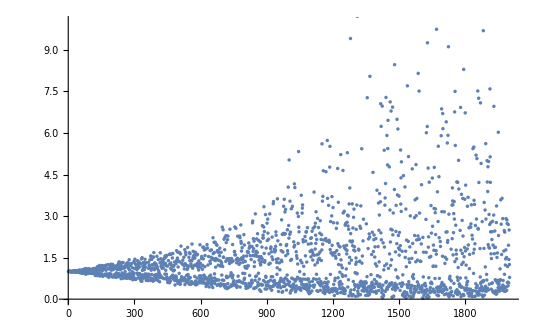

```mathematica
ListPlot[
Abs@First@#/Abs@Last@#&/@data2StepsSorted⟦All,"TargetState"⟧,
PlotRange->{All,{0,10}}
]
```

```mathematica
#⟦"WholeStates",1⟧&/@lowProbabilityEntries//Map[# Exp[-I Arg@#⟦2,1⟧]&]//Chop//Map@traditionalForm
```

{(-0.000330959+0.000111321 ⅈ | 0
0.707262 | -0.706951-0.0000981737 ⅈ
0 | -0.000331089-0.000111416 ⅈ),(0.000524397-9.85835×10^-7 ⅈ | 0
0.706941 | -0.707272+0.000204522 ⅈ
0 | 0.000524151+8.33805×10^-7 ⅈ),(-0.000747812-0.000557401 ⅈ | 0
0.707269 | -0.706943-0.000897371 ⅈ
0 | -0.000748863+0.000556707 ⅈ),(-0.000984323-0.00239347 ⅈ | 0
0.705711 | -0.70849-0.000203371 ⅈ
0 | -0.000981146+0.0023838 ⅈ)}

To see how these states are possible we look at the coin operators generating the lowest probability state.
In particular, the last one is a Pauli X matrix, consistently with the vanishing amplitudes at first and last site.

```mathematica
devolveStateAllTheWayAndGetCoins[
#⟦"WholeStates",1⟧&@lowProbabilityEntries⟦1⟧
]["Coins"]//Map@traditionalForm
```

{(0.706951 | -0.623535+0.333803 ⅈ
-0.623535-0.333803 ⅈ | -0.706951),(0.000492391-0.0000388714 ⅈ | 0.969936-0.24336 ⅈ
0.969936+0.24336 ⅈ | -0.000492391-0.0000388714 ⅈ)}

### For 3 steps, compute the probability associated with all the solutions for the d:

#### Generate/save/load data

```mathematica
data3Steps=With[{numberOfSteps=3,numberOfStatesToCompute=10000},
Block[{randomTarget,solutionsForD,wholeStateWithDs,fullStatesFromTarget,iterator=0},
Table[
iterator++;
randomTarget=RandomUnitary[numberOfSteps+1]⟦1⟧;
solutionsForD=Quiet@findDsGivingReachableState[numberOfSteps, randomTarget];
wholeStateWithDs=generalTwoColumnsStateWithD[numberOfSteps+1]/.Thread[u/@Range@Length@randomTarget->randomTarget];

(* Compute full state for every solution found for the ds *)
fullStatesFromTarget=Function[indexOfSolution,
wholeStateWithDs/.solutionsForD⟦indexOfSolution⟧//#/Norm@Flatten@#&
]/@Range@Length@solutionsForD;

(* prepare output of iteration *)
<|
"Probabilities"->projectionProbabilityFromWholeState/@fullStatesFromTarget,
"TargetState"->randomTarget,
"WholeStates"->fullStatesFromTarget
|>,
numberOfStatesToCompute
]~Monitor~iterator
]
];
data3StepsSorted=Normal@Dataset[data3Steps][SortBy[Min@#"Probabilities"&]];
```

```mathematica
FileNames@FileNameJoin@{NotebookDirectory[],"data","from solving system for d","*"}
```

{C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_2steps_10000states_201703012_2.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_2steps_10000states_201703012.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_3steps_10000states_20170312_2.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_3steps_10000states_20170312.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_4steps_10000states_20170306.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_4steps_10000states_20170312.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_5steps_1000states_aigis07_20170310.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_5steps_1000states_aigis07_20170312.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_5steps_1000states_aigis08_20170308.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_5steps_1000states_aigis08_20170309.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_5steps_1000states_aigis08_20170310.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_5steps_1000states_aigis08_20170312.mx}

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_3steps_10000states_20170312_2.mx"},data3StepsSorted,"MX"]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\statesAndProbabilities_3steps_10000states_20170312_2.mx

```mathematica
FileNames@FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_3steps*.mx"}
```

{C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_3steps_10000states_20170312_2.mx,C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\data\from solving system for d\statesAndProbabilities_3steps_10000states_20170312.mx}

```mathematica
data3StepsSorted=Join@@(Import/@FileNames@FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_3steps*.mx"});
```

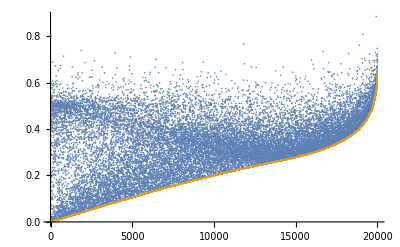

```mathematica
ListPlot[
{Max/@SortBy[Min]@data3StepsSorted⟦All,"Probabilities"⟧,
Min/@SortBy[Min]@data3StepsSorted⟦All,"Probabilities"⟧},
PlotRange->All
]
```

#### Histogram probabilities (plots in paper)

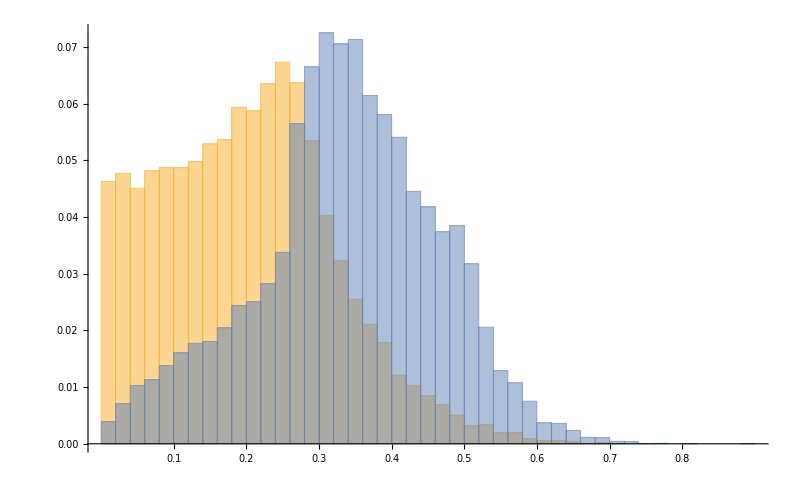

```mathematica
Histogram[
MinMax/@data3StepsSorted⟦All,"Probabilities"⟧//Transpose,
40,"Probability",
AxesStyle->texStyles["title"],ImageSize->800,
Ticks->{Range[0.1,0.8,0.1],Automatic}
]
```

```mathematica
exportHere["minMaxProjectionProbabilities_3steps_20000states_histogram40binsProbability.pdf",%265]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\minMaxProjectionProbabilities_3steps_10000states_histogram40binsProbability.pdf

```mathematica
SystemOpen@DirectoryName@%
```

```mathematica
SystemOpen@NotebookDirectory[]
```

Can’t see any particular correlation between the projection probabilities associated to the different solutions for same target states

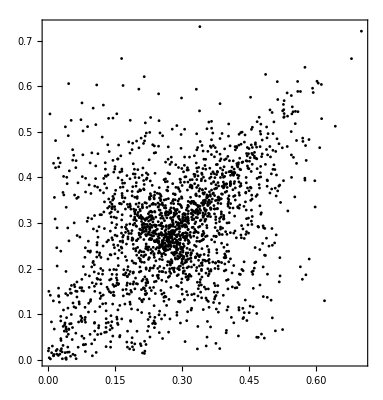

```mathematica
Graphics[{
PointSize@0.005,
Point@data3Steps⟦All,"Probabilities",{1,2}⟧
},
PlotRange->All,Frame->True
]
```

But there is some correlation between the minimum absolute value of the extremal amplitudes, and the minimal associated projection probabilities.
Generally speaking, the higher projection probabilities are associated with states that are “more distributed”

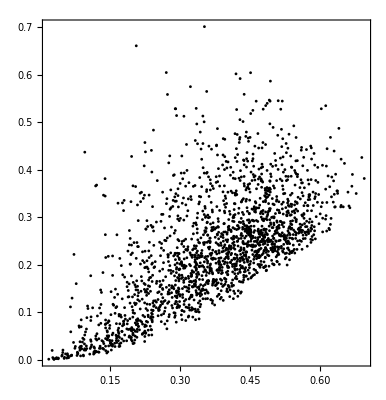

```mathematica
Graphics[{
PointSize@0.005,
Dataset[data3StepsSorted][All,{Min@Abs@#"TargetState"⟦{1,-1}⟧,Min@#"Probabilities"}&]//Normal//Point
},
PlotRange->All,Frame->True
]
```

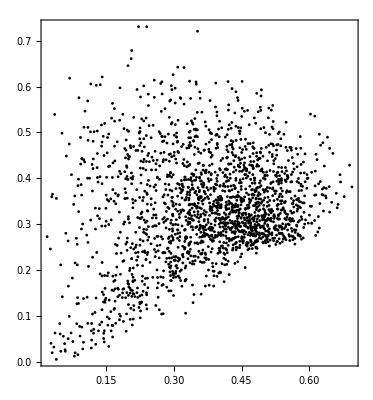

```mathematica
Graphics[{
PointSize@0.005,
Dataset[data3StepsSorted][All,{Min@Abs@#"TargetState"⟦{1,-1}⟧,Max@#"Probabilities"}&]//Normal//Point
},
PlotRange->All,Frame->True
]
```

```mathematica
lowestProbabilityEntries=Dataset[data3Steps][SortBy[Min@#Probabilities&]][1;;20]//Normal;
```

```mathematica
lowestProbabilityEntries⟦1;;4,"TargetState"⟧//Map[# Exp[-I Arg@#⟦1⟧]&]//Chop//Abs
```

{{0.746992,0.246054,0.617577,0.0076861},{0.523427,0.797814,0.299131,0.00611648},{0.00638633,0.568518,0.677195,0.467069},{0.75487,0.63865,0.148673,0.0139171}}

```mathematica
PrintDefinitions@absArgForm
```

mt58c_shm35FrontEndObject[LinkObject["mt58c_shm", 3, 1]]35utilities`absArgForm

```mathematica
Normal[Dataset[data3Steps][SortBy[-Min@#Probabilities&]][1;;10]]⟦All,"Probabilities"⟧//TableForm
```

0.679589 | 0.740783
0.578757 | 0.58033
0.560272 | 0.560244
0.567984 | 0.554726
0.558875 | 0.54482
0.55722 | 0.544016
0.557089 | 0.543242
0.522838 | 0.527542
0.531941 | 0.510907
0.663164 | 0.506056

#### Study some states associated with very low probabilities: some phenomenology.

We look at some states resulting from solving the reachability conditions from the following target states over 4 sites.
(Note that they all have a vanishing amplitude on the far left or right. This is probably no coincidence)

```mathematica
lowestProbabilityEntries⟦1;;4,"TargetState"⟧//Map[# Exp[-I Arg@#⟦1⟧]&]//Chop//absArgForm//traditionalForm
```

(0.746992 | 0.246054 ⅇ^(2.05519ⅈ) | 0.617577 ⅇ^(2.89074ⅈ) | 0.0076861 ⅇ^(2.47765ⅈ)
0.523427 | 0.797814 ⅇ^(-3.12043ⅈ) | 0.299131 ⅇ^(2.55792ⅈ) | 0.00611648 ⅇ^(-0.316337ⅈ)
0.00638633 | 0.568518 ⅇ^(0.440744ⅈ) | 0.677195 ⅇ^(0.607207ⅈ) | 0.467069 ⅇ^(2.21992ⅈ)
0.75487 | 0.63865 ⅇ^(-1.0424ⅈ) | 0.148673 ⅇ^(0.0910607ⅈ) | 0.0139171 ⅇ^(-0.300756ⅈ))

Basically all of the states associated to at least one very low projection probability have nearly vanishing amplitudes on one of the two extremal sites:

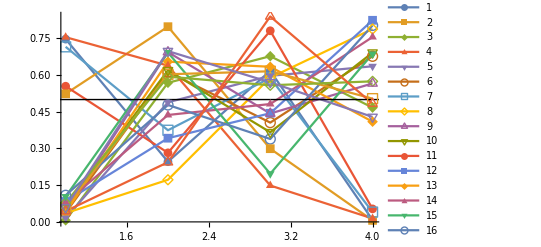

```mathematica
ListPlot[
lowestProbabilityEntries⟦1;;20,"TargetState"⟧//Map[# Exp[-I Arg@#⟦1⟧]&]//Chop//Abs,
Joined->True,PlotMarkers->Automatic,PlotRange->All,Epilog->{InfiniteLine@{{0,.5},{1,.5}}},PlotLegends->Automatic
]
```

Each one of these states corresponds to a full state giving a very low projection probability.
Note also that in most cases (all except one) there is also another solution which corresponds to a significantly higher projection probability.

```mathematica
lowestProbabilityEntries⟦All,"Probabilities"⟧//TableForm
```

0.000636472 | 0.169185 | 0.0016554 | 0.0000580899
0.000207087 | 0.000702744 | 0.415806 | 0.00215112
0.000253421 | 0.000755802 |  | 
0.000437179 | 0.514446 | 0.0009591 | 0.000563185

We now focus on the solutions for the first target state. Here are the 4 full states corresponding to the 4 solutions for the d_i:
Note how all the states associated with very low probabilities are all those with very small amplitudes on the extremal sites.

```mathematica
lowestProbabilityEntries⟦All,"WholeStates"⟧⟦1⟧//Map[# Exp[-I Arg@#⟦1,1⟧]&]//Chop//absArgForm//Map@MF
```

{(0.0266514 | 0
0.703916 ⅇ^(-1.99238ⅈ) | 0.709366 ⅇ^(1.15895ⅈ)
0.00729895 ⅇ^(-1.8229ⅈ) | 0.023203 ⅇ^(2.57073ⅈ)
0 | 0.000274227 ⅇ^(2.47765ⅈ)),(0.434521 | 0
0.523753 ⅇ^(-1.78828ⅈ) | 0.63976 ⅇ^(1.49826ⅈ)
0.00658275 ⅇ^(-2.16221ⅈ) | 0.357097 ⅇ^(2.87336ⅈ)
0 | 0.00447097 ⅇ^(2.47765ⅈ)),(0.0429815 | 0
0.712217 ⅇ^(1.60255ⅈ) | 0.699512 ⅇ^(-1.54789ⅈ)
0.00719756 ⅇ^(0.88395ⅈ) | 0.0391225 ⅇ^(3.05829ⅈ)
0 | 0.000442254 ⅇ^(2.47765ⅈ)),(0.00805158 | 0
0.706163 ⅇ^(-0.26141ⅈ) | 0.707965 ⅇ^(2.87743ⅈ)
0.00728454 ⅇ^(2.74181ⅈ) | 0.00121149 ⅇ^(-1.35297ⅈ)
0 | 0.0000828459 ⅇ^(2.47765ⅈ))}

For all of these solutions, the first coin operator is a Z gate. This is because the target state has vanishing amplitude on the last site, so the walker must go left with probability 1 at the first step.

```mathematica
devolveStateAllTheWayAndGetCoins[
lowestProbabilityEntries⟦All,"WholeStates"⟧⟦1,1⟧
]["Coins"]//Map@MF
```

{(0.999947 | -0.00232628-0.0100224 ⅈ
-0.00232628+0.0100224 ⅈ | -0.999947),(0.709904 | 0.0414638+0.703077 ⅈ
0.0414638-0.703077 ⅈ | -0.709904),(0.0354026-0.012499 ⅈ | 0.682061-0.730331 ⅈ
0.682061+0.730331 ⅈ | -0.0354026-0.012499 ⅈ)}

```mathematica
devolveStateAllTheWayAndGetCoins[
lowestProbabilityEntries⟦All,"WholeStates"⟧⟦1,2⟧
]["Coins"]//Map@MF
```

{(0.999947 | -0.00232628-0.0100224 ⅈ
-0.00232628+0.0100224 ⅈ | -0.999947),(0.773411 | 0.362566+0.519982 ⅈ
0.362566-0.519982 ⅈ | -0.773411),(0.529805-0.187049 ⅈ | 0.331204-0.758039 ⅈ
0.331204+0.758039 ⅈ | -0.529805-0.187049 ⅈ)}

We now focus on the solutions for the second target state. Here are the 4 full states corresponding to the 4 solutions for the d_i:
Note how all the states associated with very low probabilities are all those with very small amplitudes on the extremal sites.

```mathematica
lowestProbabilityEntries⟦All,"WholeStates"⟧⟦2⟧//Map[# Exp[-I Arg@#⟦1,1⟧]&]//Chop//absArgForm//Map@MF
```

{(0.0106524 | 0
0.715093 ⅇ^(3.09487ⅈ) | 0.698894 ⅇ^(-0.0483012ⅈ)
0.00816689 ⅇ^(2.87356ⅈ) | 0.00303894 ⅇ^(0.403049ⅈ)
0 | 0.000124478 ⅇ^(-0.316337ⅈ)),(0.0196232 | 0
0.70401 ⅇ^(-1.37773ⅈ) | 0.709738 ⅇ^(1.80539ⅈ)
0.0082936 ⅇ^(1.01986ⅈ) | 0.013728 ⅇ^(-3.07698ⅈ)
0 | 0.000229306 ⅇ^(-0.316337ⅈ)),(0.477328 | 0
0.421613 ⅇ^(1.90955ⅈ) | 0.71799 ⅇ^(-2.52864ⅈ)
0.00839003 ⅇ^(-0.929293ⅈ) | 0.280694 ⅇ^(2.5478ⅈ)
0 | 0.00557779 ⅇ^(-0.316337ⅈ)),(0.0343323 | 0
0.693755 ⅇ^(1.12426ⅈ) | 0.718866 ⅇ^(-2.08236ⅈ)
0.00840027 ⅇ^(-1.37557ⅈ) | 0.0262124 ⅇ^(2.32782ⅈ)
0 | 0.000401189 ⅇ^(-0.316337ⅈ))}

We now focus on the solutions for the third target state. Here are the 4 full states corresponding to the 4 solutions for the d_i:
Note how all the states associated with very low probabilities are all those with very small amplitudes on the extremal sites.

```mathematica
lowestProbabilityEntries⟦All,"WholeStates"⟧⟦3⟧//Map[# Exp[-I Arg@#⟦1,1⟧]&]//Chop//absArgForm//Map@MF
```

{(0.000143776 | 0
0.00668974 ⅇ^(1.27637ⅈ) | 0.00968058 ⅇ^(-0.0974222ⅈ)
0.707996 ⅇ^(-0.824251ⅈ) | 0.70604 ⅇ^(2.29596ⅈ)
0 | 0.0105152 ⅇ^(2.21992ⅈ)),(0.000248296 | 0
0.0181091 ⅇ^(0.00718188ⅈ) | 0.00948826 ⅇ^(1.37105ⅈ)
0.693931 ⅇ^(-2.29273ⅈ) | 0.719522 ⅇ^(0.840108ⅈ)
0 | 0.0181593 ⅇ^(2.21992ⅈ))}

#### What about the states associated to all high projection probabilities?

Notice how all these states have amplitudes well separated from zero

```mathematica
Normal[Dataset[data3Steps][SortBy[-Min@#Probabilities&]][1;;10]]⟦All,"Probabilities"⟧//TableForm
```

0.679589 | 0.740783
0.578757 | 0.58033
0.560272 | 0.560244
0.567984 | 0.554726
0.558875 | 0.54482
0.55722 | 0.544016
0.557089 | 0.543242
0.522838 | 0.527542
0.531941 | 0.510907
0.663164 | 0.506056

```mathematica
SystemOpen@NotebookDirectory[]
```

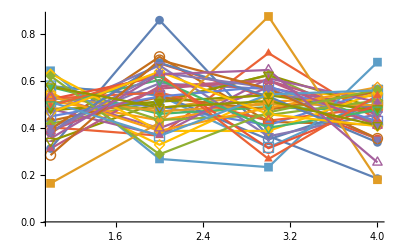

```mathematica
ListPlot[
Normal[Dataset[data3Steps][SortBy[-Min@#Probabilities&]][1;;40]]⟦All,"TargetState"⟧//Abs,
Joined->True,PlotMarkers->Automatic,PlotRange->All
]
```

#### Probabilities of reaching particular states:

```mathematica
With[{numberOfSteps=3},
Block[{
target=Normalize@ConstantArray[1,numberOfSteps+1],
ds,fullState},

ds=findDsGivingReachableState[numberOfSteps,target]⟦1⟧;
fullState=generalTwoColumnsStateWithD[numberOfSteps+1]/.ds/.Thread[u/@Range@Length@target->target]//#/Norm@Flatten@#&//Echo[#,"Full state: ",traditionalForm]&;
devolveStateAllTheWayAndGetCoins[fullState]["Coins"]//Echo[#,"Coins: ",Map@traditionalForm]&;
projectionProbabilityFromWholeState[fullState]
]
]
```

Full state:  (0.353553 | 0
0.353553+0.353553 ⅈ | 0.-0.353553 ⅈ
0.-0.353553 ⅈ | 0.353553+0.353553 ⅈ
0 | 0.353553)

Coins:  {(0.707107 | 0.707107
0.707107 | -0.707107),(0.707107 | 0.+0.707107 ⅈ
0.-0.707107 ⅈ | -0.707107),(-0.707107 | 0.-0.707107 ⅈ
0.+0.707107 ⅈ | 0.707107)}

0.25

### For 4 steps, compute the probability associated with all the solutions for the d:

#### Generate/save/load data

```mathematica
data4Steps=With[{numberOfSteps=4,numberOfStatesToCompute=10000},
Block[{randomTarget,solutionsForD,wholeStateWithDs,fullStatesFromTarget,iterator=0},
Table[
iterator++;
randomTarget=randomUnitary[numberOfSteps+1]⟦1⟧;
solutionsForD=Quiet@findDsGivingReachableState[numberOfSteps, randomTarget];
wholeStateWithDs=generalTwoColumnsStateWithD[numberOfSteps+1]/.Thread[u/@Range@Length@randomTarget->randomTarget];

(* Compute full state for every solution found for the ds *)
fullStatesFromTarget=Function[indexOfSolution,
wholeStateWithDs/.solutionsForD⟦indexOfSolution⟧//#/Norm@Flatten@#&
]/@Range@Length@solutionsForD;

(* prepare output of iteration *)
<|
"Probabilities"->projectionProbabilityFromWholeState/@fullStatesFromTarget,
"TargetState"->randomTarget,
"WholeStates"->fullStatesFromTarget
|>,
numberOfStatesToCompute
]~Monitor~iterator
]
];
data4StepsSorted=Normal@Dataset[data4Steps][SortBy[Min@#"Probabilities"&]];
```

```mathematica
data4StepsSorted//Length
```

10000

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"statesAndProbabilities_4steps_10000states_20170312.mx"},data4StepsSorted,"MX"]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\statesAndProbabilities_4steps_10000states_20170312.mx

```mathematica
data4StepsSorted=Import[FileNameJoin@{NotebookDirectory[],"data","statesAndProbabilities_4steps_10000states.mx"},"MX"];
```

#### Look at the data

```mathematica
data4StepsSorted=Join@@(Import/@FileNames[FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_4steps_*.mx"}]);
```

```mathematica
Length@data4StepsSorted
```

20000

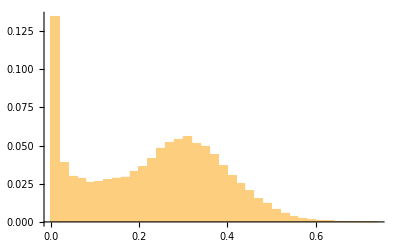

```mathematica
Histogram[
Flatten@data4StepsSorted⟦All,"Probabilities"⟧,
40,"Probability"
]
```

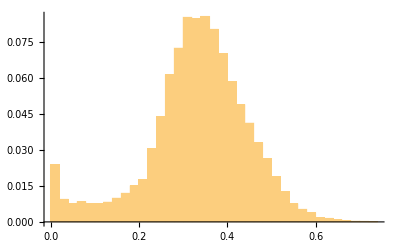

```mathematica
Histogram[
Max/@data4StepsSorted⟦All,"Probabilities"⟧,
40,"Probability"
]
```

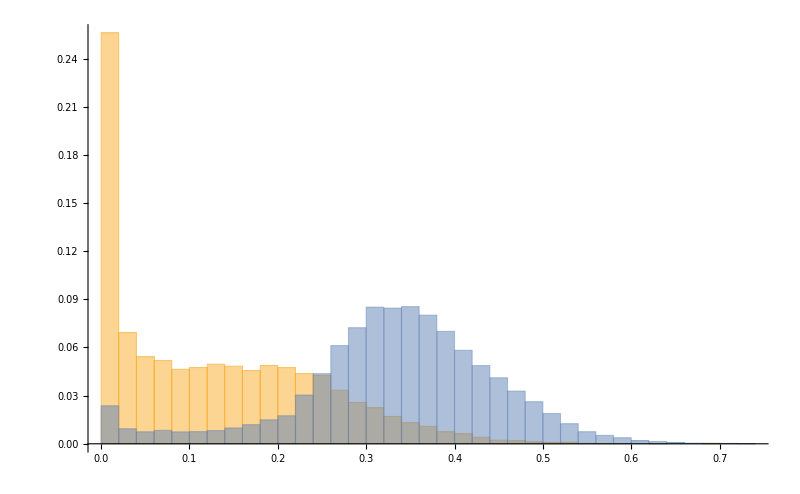

```mathematica
Histogram[
MinMax/@data4StepsSorted⟦All,"Probabilities"⟧//Transpose,
40,"Probability",
ImageSize->800,AxesStyle->texStyles["title"]
]
```

```mathematica
exportHere["minMaxProjectionProbabilities_4steps_20000states_histogram40binsProbability.pdf",%221]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\minMaxProjectionProbabilities_4steps_20000states_histogram40binsProbability.pdf

### For 5 steps, compute the probability associated with all the solutions for the d:

For 5 steps, it takes ≃1 minute to solve the system for a single state (on the laptop).

#### Generate/save/load data

```mathematica
ParallelEvaluate[<<manyBosonStates`]
```

Permanent::removed: (caveat) the function System`Permanent[_] has been removed; the new function PermanentCode`Permanent[_] compatibly replaces it (with faster evaluation).

{Null,Null,Null,Null}

```mathematica
data5Steps=With[{numberOfSteps=5,numberOfStatesToCompute=8},
Block[{randomTarget,solutionsForD,wholeStateWithDs,fullStatesFromTarget},
ParallelTable[
randomTarget=randomUnitary[numberOfSteps+1]⟦1⟧;
solutionsForD=Quiet@findDsGivingReachableState[numberOfSteps, randomTarget];
wholeStateWithDs=generalTwoColumnsStateWithD[numberOfSteps+1]/.Thread[u/@Range@Length@randomTarget->randomTarget];

(* Compute full state for every solution found for the ds *)
fullStatesFromTarget=Function[indexOfSolution,
wholeStateWithDs/.solutionsForD⟦indexOfSolution⟧//#/Norm@Flatten@#&
]/@Range@Length@solutionsForD;

(* prepare output of iteration *)
<|
"Probabilities"->projectionProbabilityFromWholeState/@fullStatesFromTarget,
"TargetState"->randomTarget,
"WholeStates"->fullStatesFromTarget
|>,
numberOfStatesToCompute
]
]
];
data5StepsSorted=Normal@Dataset[data5Steps][SortBy[Min@#"Probabilities"&]];
```

```mathematica
findDsGivingReachableState[5,randomUnitary[6]⟦1⟧]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{d[2]→-0.530705-0.0403061 ⅈ,d[3]→-0.0130131+0.113848 ⅈ,d[4]→-0.669972+0.235649 ⅈ,d[5]→0.0100937-0.0804789 ⅈ},{d[2]→-0.387619-0.511918 ⅈ,d[3]→-0.320475-0.268591 ⅈ,d[4]→0.141951-0.162537 ⅈ,d[5]→-0.109111+0.364195 ⅈ},{d[2]→-0.208744+0.0749848 ⅈ,d[3]→0.834323-0.140934 ⅈ,d[4]→0.131174+0.264981 ⅈ,d[5]→0.322352-0.0130669 ⅈ},{d[2]→-0.0353054-0.206933 ⅈ,d[3]→-0.504732+0.0922596 ⅈ,d[4]→-0.792978-0.562856 ⅈ,d[5]→0.32082+0.296122 ⅈ},{d[2]→0.122779+0.340265 ⅈ,d[3]→-0.239447-0.251415 ⅈ,d[4]→0.0784382-0.19981 ⅈ,d[5]→0.716203-0.0599051 ⅈ},{d[2]→0.249195-0.0871116 ⅈ,d[3]→0.154681+0.45601 ⅈ,d[4]→-0.246455-0.0579008 ⅈ,d[5]→0.605602+0.341457 ⅈ}}

#### Look at the data

```mathematica
data5steps=Join@@(Import/@FileNames[FileNameJoin@{NotebookDirectory[],"data","from solving system for d","statesAndProbabilities_5steps_*.mx"}]);
```

```mathematica
data5steps⟦1⟧
```

<|Probabilities→{1.3182×10^-6,4.1943×10^-7,2.09097×10^-6,2.33354×10^-6,0.00328871,0.00484671,0.186365,0.0177255,0.0502289,1.62438×10^-6,4.23544×10^-6,2.70859×10^-6},TargetState→{0.00521295-0.0194391 ⅈ,-0.213187+0.547246 ⅈ,0.059037-0.0135923 ⅈ,-0.208342-0.434644 ⅈ,-0.0964223+0.225337 ⅈ,-0.127456+0.585112 ⅈ},WholeStates→{{{8.46428×10^-6-0.0000315633 ⅈ,0.},{0.000639058+0.000611944 ⅈ,-0.000985211+0.000276621 ⅈ},{0.00245856+0.0302594 ⅈ,-0.00236271-0.0302815 ⅈ},{-0.634715+0.308686 ⅈ,0.634376-0.309392 ⅈ},{0.022274+0.0207592 ⅈ,-0.0224305-0.0203933 ⅈ},{0.,-0.000206951+0.000950048 ⅈ}},{{4.77451×10^-6-0.0000178041 ⅈ,0.},{0.0000250161-0.000280959 ⅈ,-0.000220273+0.000782178 ⅈ},{0.00508631-0.0235275 ⅈ,-0.00503224+0.0235151 ⅈ},{0.144692-0.691486 ⅈ,-0.144883+0.691088 ⅈ},{-0.00485042+0.0236869 ⅈ,0.00476211-0.0234806 ⅈ},{0.,-0.000116736+0.000535901 ⅈ}},{{0.0000106604-0.0000397525 ⅈ,0.},{-7.11293×10^-6+0.000618849 ⅈ,-0.00042885+0.000500257 ⅈ},{-0.0184866+0.00574871 ⅈ,0.0186074-0.0057765 ⅈ},{-0.615301-0.348168 ⅈ,0.614875+0.347279 ⅈ},{0.00451178+0.0190794 ⅈ,-0.00470897-0.0186186 ⅈ},{0.,-0.000260645+0.00119654 ⅈ}},{{0.0000112618-0.0000419951 ⅈ,0.},{-0.0000385317+0.00114319 ⅈ,-0.000422026+0.0000390507 ⅈ},{0.00667247-0.0107148 ⅈ,-0.00654493+0.0106855 ⅈ},{0.16478+0.686884 ⅈ,-0.16523-0.687823 ⅈ},{0.0106255+0.00679194 ⅈ,-0.0108338-0.00630513 ⅈ},{0.,-0.000275349+0.00126404 ⅈ}},{{0.000422777-0.00157653 ⅈ,0.},{-0.0086909+0.0219573 ⅈ,-0.00859886+0.022425 ⅈ},{0.00229556+0.00127099 ⅈ,0.00249241-0.00237334 ⅈ},{-0.00797401+0.00657492 ⅈ,-0.00892279-0.0418251 ⅈ},{-0.0786818+0.710269 ⅈ,0.0708618-0.691994 ⅈ},{0.,-0.0103368+0.0474533 ⅈ}},{{0.000513242-0.00191388 ⅈ,0.},{-0.0175199+0.0592956 ⅈ,-0.00346948-0.00541636 ⅈ},{-0.100159-0.172764 ⅈ,0.105971+0.171426 ⅈ},{0.616433+0.127457 ⅈ,-0.636945-0.17025 ⅈ},{0.165651-0.0958607 ⅈ,-0.175144+0.118046 ⅈ},{0.,-0.0125487+0.0576073 ⅈ}},{{0.00318259-0.0118679 ⅈ,0.},{-0.138509+0.340488 ⅈ,0.00835469-0.00638536 ⅈ},{0.305589-0.169069 ⅈ,-0.269546+0.160771 ⅈ},{-0.357572-0.216636 ⅈ,0.230376-0.0487215 ⅈ},{-0.133757-0.282847 ⅈ,0.0748898+0.420418 ⅈ},{0.,-0.077814+0.35722 ⅈ}},{{0.000981516-0.00366007 ⅈ,0.},{-0.0444431+0.0949982 ⅈ,0.00430332+0.0080397 ⅈ},{0.0898004+0.236797 ⅈ,-0.0786847-0.239356 ⅈ},{0.543811+0.160775 ⅈ,-0.583038-0.242611 ⅈ},{-0.223499+0.153842 ⅈ,0.205344-0.111415 ⅈ},{0.,-0.023998+0.110167 ⅈ}},{{0.00165225-0.00616123 ⅈ,0.},{-0.0759652+0.178805 ⅈ,0.00839529-0.00535458 ⅈ},{0.294026-0.131049 ⅈ,-0.275314+0.126741 ⅈ},{-0.508881-0.237639 ⅈ,0.442847+0.0998776 ⅈ},{-0.148898-0.256147 ⅈ,0.118337+0.327567 ⅈ},{0.,-0.0403973+0.185452 ⅈ}},{{9.39599×10^-6-0.0000350376 ⅈ,0.},{-0.000451701+0.000402379 ⅈ,0.0000674451+0.000583996 ⅈ},{0.0115812+0.01287 ⅈ,-0.0114748-0.0128945 ⅈ},{0.704878-0.0481814 ⅈ,-0.705254+0.047398 ⅈ},{-0.0097531+0.0145205 ⅈ,0.00957931-0.0141143 ⅈ},{0.,-0.000229731+0.00105463 ⅈ}},{{0.0000151722-0.0000565769 ⅈ,0.},{-0.000941161+0.00133208 ⅈ,0.000320685+0.000260665 ⅈ},{-0.000771181-0.0120907 ⅈ,0.000943006+0.0120512 ⅈ},{-0.433808+0.557738 ⅈ,0.433201-0.559003 ⅈ},{-0.0120363+0.00251559 ⅈ,0.0117556-0.00185975 ⅈ},{0.,-0.000370958+0.00170296 ⅈ}},{{0.0000121331-0.0000452442 ⅈ,0.},{-0.00131377+0.000401818 ⅈ,0.000817576+0.00087189 ⅈ},{-0.0163694+0.0312806 ⅈ,0.0165068-0.0313122 ⅈ},{0.460038+0.533945 ⅈ,-0.460523-0.534957 ⅈ},{-0.0335155+0.0118953 ⅈ,0.0332911-0.0113708 ⅈ},{0.,-0.000296652+0.00136184 ⅈ}}}|>

```mathematica
data5steps//Length
```

6000

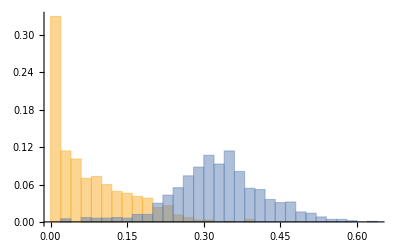
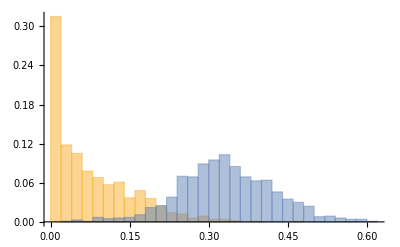
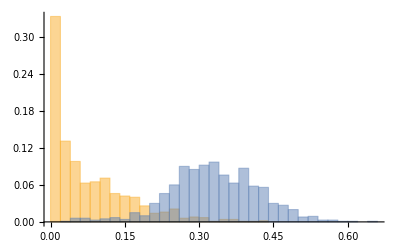
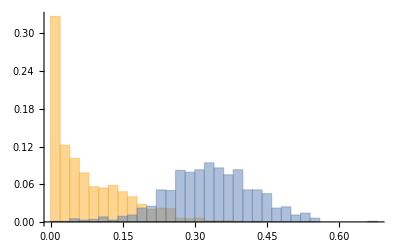
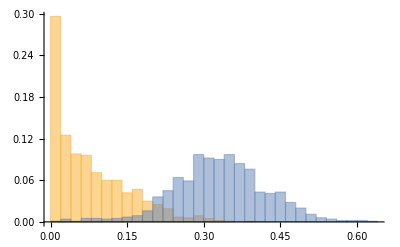
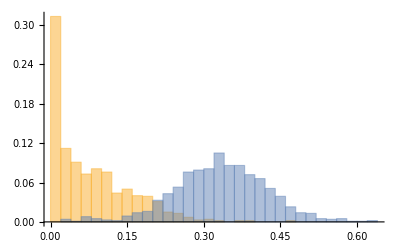

```mathematica
Table[
Histogram[
Transpose[MinMax/@dataBatch⟦All,"Probabilities"⟧],
40,"Probability"
],
{dataBatch,data5steps}
]
```

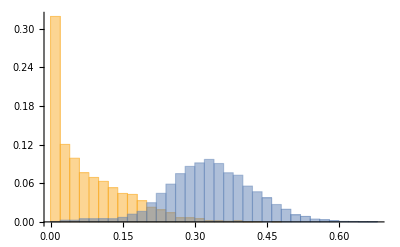

```mathematica
Histogram[
Transpose[MinMax/@Apply[Join,data5steps]⟦All,"Probabilities"⟧],
40,"Probability"
]
```

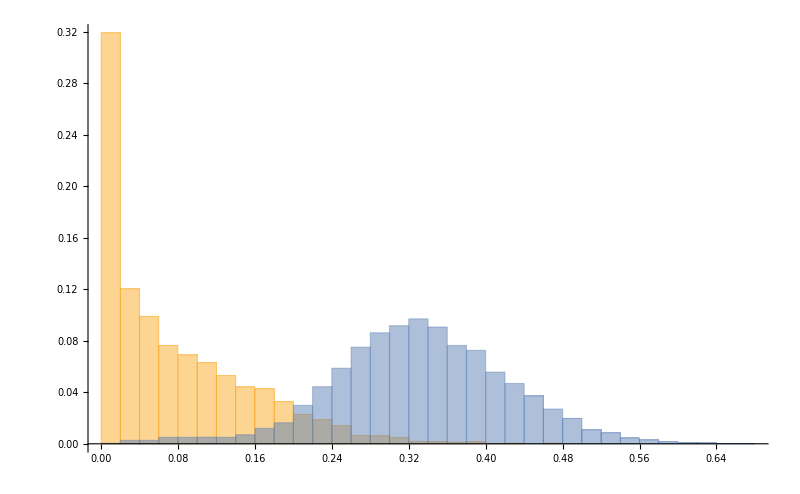

```mathematica
Histogram[
MinMax/@Apply[Join,data5steps]⟦All,"Probabilities"⟧//Transpose,
40,"Probability",
ImageSize->800,AxesStyle->texStyles["title"]
]
```

```mathematica
exportHere["minMaxProjectionProbabilities_5steps_6000states_histogram40bins&probability.pdf",%178]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\minMaxProjectionProbabilities_5steps_6000states_histogram40bins&probability.pdf

```mathematica
SystemOpen@DirectoryName@%
```

#### Stability analysis

The stability seems to be clearly linked to the projection probability: states obtained with almost vanishing probabilities are extremely unstable, while the others are decently stable

```mathematica
Echo[data5steps⟦1⟧["Probabilities"],"Probabilities:"];
With[{data=data5steps⟦1⟧,stateToLook=10},
stabilityAnalysis`plotFidelityVsParameters[
Chop@Reverse@reachabilitySolutions`computeCoinParameters[data,stateToLook],
data["TargetState"],
{-.01,.01},
"TypeOfPerturbation"->Plus,
PlotRange->All,ImageSize->Large
]
]
```

Probabilities: {1.3182×10^-6,4.1943×10^-7,2.09097×10^-6,2.33354×10^-6,0.00328871,0.00484671,0.186365,0.0177255,0.0502289,1.62438×10^-6,4.23544×10^-6,2.70859×10^-6}

-Graphics-

```mathematica
Echo[data5steps⟦1⟧["Probabilities"],"Probabilities:"];
With[{data=data5steps⟦1⟧,stateToLook=5},
stabilityAnalysis`plotFidelityVsParameters[
Chop@Reverse@reachabilitySolutions`computeCoinParameters[data,stateToLook],
data["TargetState"],
{-.01,.01},
"TypeOfPerturbation"->Plus,
PlotRange->All,ImageSize->Large
]
]
```

Probabilities: {1.3182×10^-6,4.1943×10^-7,2.09097×10^-6,2.33354×10^-6,0.00328871,0.00484671,0.186365,0.0177255,0.0502289,1.62438×10^-6,4.23544×10^-6,2.70859×10^-6}

-Graphics-

```mathematica
Echo[data5steps⟦1⟧["Probabilities"],"Probabilities:"];
With[{data=data5steps⟦1⟧,stateToLook=10},
stabilityAnalysis`plotFidelityVsParameters[
Chop@Reverse@reachabilitySolutions`computeCoinParameters[data,stateToLook],
data["TargetState"],
{0.9,1.1},
"TypeOfPerturbation"->Times,
PlotRange->All,ImageSize->Large
]
]
```

Probabilities: {1.3182×10^-6,4.1943×10^-7,2.09097×10^-6,2.33354×10^-6,0.00328871,0.00484671,0.186365,0.0177255,0.0502289,1.62438×10^-6,4.23544×10^-6,2.70859×10^-6}

-Graphics-

```mathematica
Echo[data5steps⟦1⟧["Probabilities"],"Probabilities:"];
With[{data=data5steps⟦1⟧,stateToLook=5},
stabilityAnalysis`plotFidelityVsParameters[
Chop@Reverse@reachabilitySolutions`computeCoinParameters[data,stateToLook],
data["TargetState"],
{0.9,1.1},
"TypeOfPerturbation"->Times,
PlotRange->All,ImageSize->Large
]
]
```

Probabilities: {1.3182×10^-6,4.1943×10^-7,2.09097×10^-6,2.33354×10^-6,0.00328871,0.00484671,0.186365,0.0177255,0.0502289,1.62438×10^-6,4.23544×10^-6,2.70859×10^-6}

-Graphics-

Take a state and see the stability plots for all its solutions

```mathematica
Echo[data5StepsSorted⟦100⟧["Probabilities"],"Probabilities:"];
```

```mathematica
data5StepsSorted⟦100,"TargetState"⟧//normalizePhase//MF
```

(0.052524
-0.0777209+0.602811 ⅈ
-0.524031+0.188887 ⅈ
-0.302246+0.362698 ⅈ
0.181683+0.0988754 ⅈ
0.0423214-0.223728 ⅈ)

```mathematica
reachabilitySolutions`computeCoinParameters@data5StepsSorted⟦100⟧//Map@MF
```

{(1.47253 | 0.913281 | 0.202771
0.376896 | 0 | 0.59136
1.24964 | 0 | -1.93702
1.13081 | 0 | -1.09464
1.34409 | 0 | 2.69887),(1.46181 | 0.913281 | 0.957496
0.367416 | 0 | 1.51274
1.2654 | 0 | 1.1237
1.07069 | 0 | -2.92468
1.34409 | 0 | 2.69887),(1.39818 | 0.913281 | 0.509285
0.715926 | 0 | 0.975409
0.141371 | 0 | 0.638131
0.238806 | 0 | 0.668757
1.34409 | 0 | 2.69887),(1.36147 | 0.913281 | 0.0872058
0.992224 | 0 | 1.32731
1.2744 | 0 | 1.56014
0.910568 | 0 | 0.407109
1.34409 | 0 | 2.69887),(1.33989 | 0.913281 | 0.99777
1.12021 | 0 | 0.836486
1.23891 | 0 | -2.44548
0.91356 | 0 | 1.8798
1.34409 | 0 | 2.69887),(0.848809 | 0.913281 | 0.488112
0.424319 | 0 | 2.43394
0.568095 | 0 | 0.526027
1.14757 | 0 | 1.20891
1.34409 | 0 | 2.69887),(0.173499 | 0.913281 | -0.632391
0.844828 | 0 | 0.254005
0.368542 | 0 | 2.0925
1.2147 | 0 | 1.19857
1.34409 | 0 | 2.69887),(0.740372 | 0.913281 | 1.99484
0.437953 | 0 | 1.9933
0.31082 | 0 | -2.43421
1.21498 | 0 | 1.37302
1.34409 | 0 | 2.69887)}

```mathematica
Get[FileNameJoin@{NotebookDirectory[],"stabilityAnalysis.m"}];
Table[
With[{data=data5StepsSorted⟦100⟧,stateToLook=n},
fig=stabilityAnalysis`plotFidelityVsParameters[
Chop@Reverse@reachabilitySolutions`computeCoinParameters[data,stateToLook],
data["TargetState"],
{-0.1,.1},
"TypeOfPerturbation"->Plus,
PlotRange->All,ImageSize->Large,
(*PlotLabel->data["Probabilities"]⟦n⟧,*)
AxesStyle->texStyles["title"]
];
exportHere[
"fidVsParameters_5stepsAnalytical_100thState_prob"<>ToString@data["Probabilities"]⟦n⟧<>".pdf",
fig
];
fig
],
{n,1,6}
]~Monitor~n
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}